```mathematica
allKeysWith5Nodes=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];
```

```mathematica
Length[allKeysWith5Nodes]
```

1024

```mathematica
allKeysWith5NodesAnd1Edge=Select[allKeysWith5Nodes,EdgeCount[allGraphs5[#,"graph"]]==1&]
```

{19683,6561,2187,729,243,81,27,9,3,1}

```mathematica
Length[allKeysWith5NodesAnd1Edge]
```

10

```mathematica
Table[
ShowGraph5Least[k]
,{k, allKeysWith5NodesAnd1Edge}
]
```

{-Graphics-1968321,-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121}

## Now compute the rank of these vectors

```mathematica
Table[
MatrixRank[
Table[
BaseCoeff[k,base]
,{k, allKeysWith5NodesAnd1Edge}
]
]
,{base,Keys[Bases]}
]
```

{10,10,10,10,10}

```mathematica
Table[
MatrixRank[
Table[
BaseCoeff[k,base]
,{k, Take[allKeysWith5Nodes,-20]}
]
]
,{base,Keys[Bases]}
]
```

{12,12,12,12,12}

```mathematica
Table[
ShowGraph5Least[k]
,{k, Take[allKeysWith5Nodes,-20]}
]
```

{-Graphics-945,-Graphics-9110,-Graphics-8416,-Graphics-8510,-Graphics-8215,-Graphics-2724,-Graphics-3615,-Graphics-3912,-Graphics-406,-Graphics-379,-Graphics-3018,-Graphics-3112,-Graphics-2815,-Graphics-921,-Graphics-1216,-Graphics-138,-Graphics-1013,-Graphics-324,-Graphics-416,-Graphics-121}

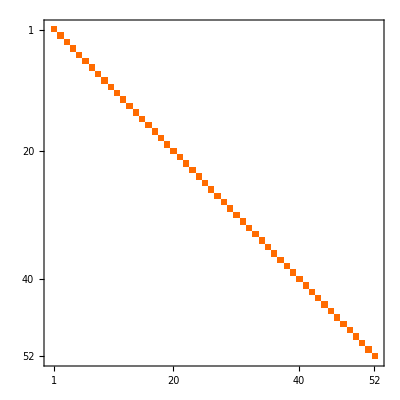

```mathematica
Table[
LatticeReduce[
Table[
BaseCoeff[k,base]
,{k, allKeysWith5Nodes}
]
]//MatrixPlot
,{base,{"E"}}
]
```

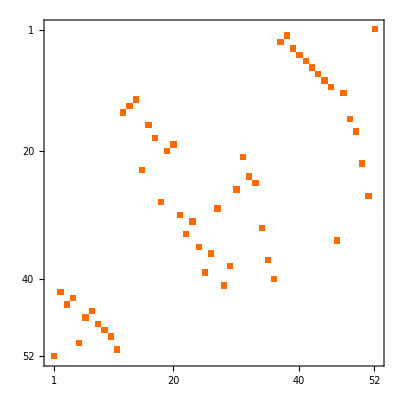

```mathematica
LatticeReduce[ConversionMatrix["E","C"]]//MatrixPlot
```

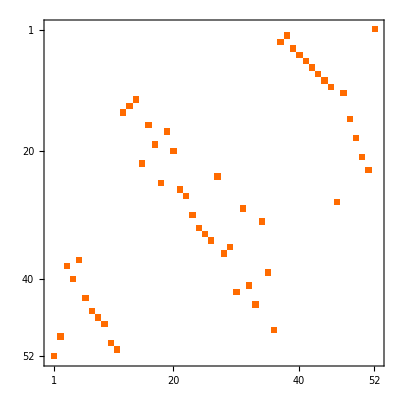

```mathematica
LatticeReduce[ConversionMatrix["C","E"]]//MatrixPlot
```

## Now compute the rank of these vectors

```mathematica
baseList=Table[
BaseCoeff[k,"C"]
,{k, Take[allGraphs5GeneratorAtomKeys,10]}
]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
MatrixRank[baseList]
```

10

```mathematica
Select[Keys[allGraphs5],MatrixRank[Append[baseList,BaseCoeff[#,"C"]]]==10&]
```

{29520,29523,29524,29525,29527,29521,29533,29514,29515,29512,29551,29493,29496,29497,29494,29605,29442,29443,29433,29434,29416,29767,29281,29278,29272,29269,29254,29200,29173,31711,27336,27337,27327,27328,27255,27256,27246,27247,36085,22963,22960,22954,22951,22720,22717,22711,22708,20776,49207,9841,9814,9760,9733,9598,9571,9517,9490,7654,3280,1093}

```mathematica
baseList2=Join[baseList,
Map[BaseCoeff[#,"C"]&,Select[Keys[allGraphs5],MatrixRank[Append[baseList,BaseCoeff[#,"C"]]]==10&]]];
```

```mathematica
Select[Keys[allGraphs5],MatrixRank[Append[baseList2,BaseCoeff[#,"C"]]]==10&]
```

{29520,29523,29524,29525,29527,29521,29533,29514,29515,29512,29551,29493,29496,29497,29494,29605,29442,29443,29433,29434,29416,29767,29281,29278,29272,29269,29254,29200,29173,31711,27336,27337,27327,27328,27255,27256,27246,27247,36085,22963,22960,22954,22951,22720,22717,22711,22708,20776,49207,9841,9814,9760,9733,9598,9571,9517,9490,7654,3280,1093}

```mathematica
Table[
ShowGraph5Least[k]
,{k, Select[Keys[allGraphs5],MatrixRank[Append[baseList,BaseCoeff[#,"C"]]]==10&]}
]
```

{-Graphics-295200,-Graphics-295230,-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295210,-Graphics-295330,-Graphics-295140,-Graphics-295150,-Graphics-295120,-Graphics-295510,-Graphics-294930,-Graphics-294960,-Graphics-294970,-Graphics-294940,-Graphics-296050,-Graphics-294420,-Graphics-294430,-Graphics-294330,-Graphics-294340,-Graphics-294160,-Graphics-297670,-Graphics-292810,-Graphics-292780,-Graphics-292720,-Graphics-292690,-Graphics-292540,-Graphics-292000,-Graphics-291730,-Graphics-317110,-Graphics-273360,-Graphics-273370,-Graphics-273270,-Graphics-273280,-Graphics-272550,-Graphics-272560,-Graphics-272460,-Graphics-272470,-Graphics-360850,-Graphics-229630,-Graphics-229600,-Graphics-229540,-Graphics-229510,-Graphics-227200,-Graphics-227170,-Graphics-227110,-Graphics-227080,-Graphics-207760,-Graphics-492070,-Graphics-98410,-Graphics-98140,-Graphics-97600,-Graphics-97330,-Graphics-95980,-Graphics-95710,-Graphics-95170,-Graphics-94900,-Graphics-76540,-Graphics-32800,-Graphics-10930}

```mathematica
Table[
MatrixRank[Append[baseList,BaseCoeff[k,"C"]]]
,
{k,Keys[allGraphs5]}
]
```

{11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,11,11,11,11,10,11,11,11,11,11,11,11,11,10,11,11,10,11}

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&&EdgeQ[allGraphs5[#,"graph"],1<->3]&&EdgeQ[allGraphs5[#,"graph"],2<->3]&]}]]
```

17

```mathematica
BellB[5]-BellB[4]
```

37

```mathematica
BellB[5]-BellB[4]-BellB[4]-BellB[4]+BellB[3]+BellB[3]
```

17

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&&EdgeQ[allGraphs5[#,"graph"],1<->3]&]}]]
```

27

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

37

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[allKeysWith5Nodes,!EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

47

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[allKeysWith5Nodes,!(EdgeQ[allGraphs5[#,"graph"],1<->2])&&!(EdgeQ[allGraphs5[#,"graph"],1<->3])&]}]]
```

40

```mathematica
MatrixRank[Table[BaseCoeff[k,"G"],{k,Select[allKeysWith5Nodes,!(EdgeQ[allGraphs5[#,"graph"],1<->2])&&!(EdgeQ[allGraphs5[#,"graph"],1<->3])&]}]]
```

40

```mathematica
MatrixRank[Table[BaseCoeff[k,"E"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

37

```mathematica
MatrixRank[Table[BaseCoeff[k,"F"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

37

```mathematica
MatrixRank[Table[BaseCoeff[k,"T"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

37

```mathematica
MatrixRank[Table[BaseCoeff[k,"G"],{k,Select[allKeysWith5Nodes,EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

37

```mathematica
Table[BellB[k],{k,5}]
```

{1,2,5,15,52}

```mathematica
MatrixRank[Table[BaseCoeff[k,"G"],{k,Select[Keys[allGraphs5],!MemberQ[allGraphs5[#,"vertexsets"],{1}]||!MemberQ[allGraphs5[#,"vertexsets"],{2}]&]}]]
```

47

```mathematica
MatrixRank[Table[BaseCoeff[k,"G"],{k,Select[Keys[allGraphs5],MemberQ[allGraphs5[#,"vertexsets"],{1,3}]&]}]]
```

15

```mathematica
BaseCoeff[K5Key,"G"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MatrixRank[{BaseCoeff[K5Key,"G"],Table[0,{k,52}]}]
```

1

```mathematica
MatrixRank[{Table[0,{k,52}],Table[0,{k,52}]}]
```

0